# Quantum Random Walk: Computationally Efficient Approach

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

This is a more efficient implementation of the quantum random walk. The price is that is less "elegant" than the naive implementation, in the sense that some operators are not defined the way you do it in a handwritten quantum calculation.

The quantum random walker (Y. Aharonov, L. Davidovich, and N. Zagury "Quantum random walks" Phys. Rev. A 48, 1687 - 1690 (1993)) is made of a "coin" and a "walker", each one with its own state-space, which will make a composite system with the coin and the walker in entanglement. A unitary operator will be defined to "flip the coin", while another unitary operator will be defined to "move the walker" based on coin's result. The second operator produces entanglement between coin and walker.

## Load the Package

First load the Quantum`Notation` package. Write:
Needs["Quantum`Notation`"];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package:

```mathematica
Needs["Quantum`Notation`"]
```

Quantum`Notation` Version 2.2.0. (July 2010) 
A Mathematica package for Quantum calculations in Dirac bra-ket notation
by José Luis Gómez-Muñoz

Execute SetQuantumAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetQuantumAliases[] must be executed again in each new notebook that is created, only one time per notebook.

In order to use the keyboard to enter quantum objects write:
SetQuantumAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetQuantumAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetQuantumAliases[];
```

## Quantum Random Walk using fast Mathematica commands

The coin C can have only two states, 0 and 1 (head and tail), while the walker P can be in any (discrete) position from -steps to steps. The coin is inially in state 0 and the walker is initially at the origin 0:

```mathematica
|w[0]⟩=|Subscript[0, ĉ]⟩⊗|Subscript[0, p̂]⟩
```

|0_(ĉ),0_(p̂)⟩

Here we define the "fliping coin" operator, which in this case is a Hadamard operator, but it could be any unitary operator that acts only in the coin C. The coin can have only two states, 0 and 1 (head and tail). Notice the last sign is negative:

```mathematica
h=1/(√2)(|Subscript[0, ĉ]⟩·⟨Subscript[0, ĉ]|+|Subscript[1, ĉ]⟩·⟨Subscript[0, ĉ]|+|Subscript[0, ĉ]⟩·⟨Subscript[1, ĉ]|-|Subscript[1, ĉ]⟩·⟨Subscript[1, ĉ]|)
```

(|0_(ĉ)⟩·⟨0_(ĉ)|+|1_(ĉ)⟩·⟨0_(ĉ)|+|0_(ĉ)⟩·⟨1_(ĉ)|-|1_(ĉ)⟩·⟨1_(ĉ)|)/(√2)

This is one of the "effcient" parts of this implementation: After "flipping the coin" the walker is moved using the Mathematica ReplaceAll[] command. This evaluation does not produce any output, however the evolution of the system is calculted and stored in |w[0]⟩, |w[1]⟩,...,|w[20]⟩

```mathematica
steps=20;
Do[
|w[k]⟩=
Expand[ReplaceAll[h·|w[k-1]⟩,
{|Subscript[0, ĉ],Subscript[j_, p̂]⟩:>|Subscript[0, ĉ],Subscript[(j-1), p̂]⟩,|Subscript[1, ĉ],Subscript[j_, p̂]⟩:>|Subscript[1, ĉ],Subscript[(j+1), p̂]⟩ }]],{k,1,steps,1}
]
```

Each state of the composite system coin-walker is stored. For example this is the state at the second step:

```mathematica
|w[2]⟩
```

1/2 |0_(ĉ),(-2)_(p̂)⟩+1/2 |0_(ĉ),0_(p̂)⟩+1/2 |1_(ĉ),0_(p̂)⟩-1/2 |1_(ĉ),2_(p̂)⟩

And this is the state at the fifth step:

```mathematica
|w[5]⟩
```

(|0_(ĉ),(-5)_(p̂)⟩)/(4 √2)+(|0_(ĉ),(-3)_(p̂)⟩)/(√2)-(|0_(ĉ),3_(p̂)⟩)/(4 √2)+(|1_(ĉ),(-3)_(p̂)⟩)/(4 √2)+(|1_(ĉ),(-1)_(p̂)⟩)/(2 √2)-(|1_(ĉ),1_(p̂)⟩)/(2 √2)+(|1_(ĉ),3_(p̂)⟩)/(2 √2)+(|1_(ĉ),5_(p̂)⟩)/(4 √2)

Here we calculate the probabilities for each walker position. This is another "efficient" part of this implementation:

```mathematica
prob=Table[
{j,
ketList=Cases[|w[steps]⟩,x_.*|Subscript[y_, ĉ],Subscript[j, p̂]⟩];
braList=Cases[⟨w[steps]|,x_.*⟨Subscript[y_, ĉ],Subscript[j, p̂]|];
productList=MapThread[Function[{b,k},b·k],{braList,ketList}];
Apply[Plus,productList]
},
{j,-steps,steps}
]
```

{{-20,1/1048576},{-19,0},{-18,181/524288},{-17,0},{-16,9257/524288},{-15,0},{-14,95617/524288},{-13,0},{-12,295265/1048576},{-11,0},{-10,965/32768},{-9,0},{-8,2501/32768},{-7,0},{-6,2377/32768},{-5,0},{-4,11221/262144},{-3,0},{-2,4165/131072},{-1,0},{0,3969/131072},{1,0},{2,3969/131072},{3,0},{4,7301/262144},{5,0},{6,637/32768},{7,0},{8,485/32768},{9,0},{10,1361/32768},{11,0},{12,28097/1048576},{13,0},{14,33317/524288},{15,0},{16,5417/524288},{17,0},{18,145/524288},{19,0},{20,1/1048576}}

Here is a plot of the probabilities for each position of the walker.

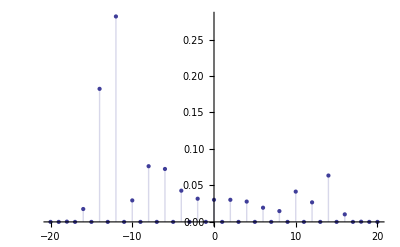

```mathematica
ListPlot[prob,PlotRange->All,Filling->Axis]
```

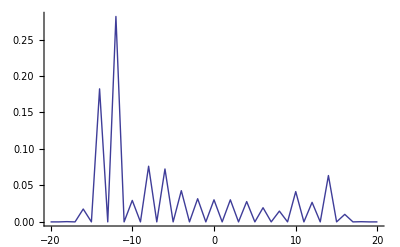

```mathematica
ListPlot[prob,PlotRange->All,Joined->True]
```

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx